# diving wave in factorized VTI media

## the diving-wave ray trajectory

#### perturbation in vertical velocity

```mathematica
Clear["Global`*"]
```

```mathematica
vz=v0+G*z;
```

```mathematica
gama=Simplify[vz/v0];
```

```mathematica
vn0=Sqrt[1+2*delta]*v0;
```

```mathematica
fa0=1-2*eta*p^2*vn0^2;
```

```mathematica
bfa0=1-(1+2*eta)*p^2*vn0^2;
```

```mathematica
fa1=Simplify[1-2*eta*p^2*vn0^2*gama^2];
```

```mathematica
bfa1=1-(1+2*eta)*p^2*vn0^2*gama^2;
```

```mathematica
Rl=x==(1+2delta)*Simplify[z*p*v0*(gama+1)/(Sqrt[fa0*fa1]*(Sqrt[bfa0*fa1]+Sqrt[fa0*bfa1]))]/.delta->(epslion-eta)/(1+2 eta)
```

x==((1+(2 (epslion-eta))/(1+2 eta)) p z (2 v0+G z))/(√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2)) (√((1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))+√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))))

```mathematica
Rr=2*((√(1-(1+2 delta) (1+2 eta) p^2 v0^2))/(G p √(1-2 (1+2 delta) eta p^2 v0^2)))-x==((1+2 delta) p z (2 v0+G z))/(√((1-2 (1+2 delta) eta p^2 v0^2) (1-2 (1+2 delta) eta p^2 (v0+G z)^2)) (√((1-(1+2 delta) (1+2 eta) p^2 v0^2) (1-2 (1+2 delta) eta p^2 (v0+G z)^2))+√((1-2 (1+2 delta) eta p^2 v0^2) (1-(1+2 delta) (1+2 eta) p^2 (v0+G z)^2))))/.delta->(epslion-eta)/(1+2 eta)
```

(2 √(1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2))/(G p √(1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2))-x==((1+(2 (epslion-eta))/(1+2 eta)) p z (2 v0+G z))/(√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2)) (√((1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))+√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))))

```mathematica
param={v0->2,G->0.5,p->0.25,epslion->0.2,eta->0.2}
```

{v0→2,G→0.5,p→0.25,epslion→0.2,eta→0.2}

```mathematica
Rl/.param/.z->-k
```

x==-(0.263523 (4-0.5 k) k)/((0.948683 √(1-0.0875 (2-0.5 k)^2)+0.806226 √(1-0.025 (2-0.5 k)^2)) √(1-0.025 (2-0.5 k)^2))

```mathematica
Rr/.param/.z->-k
```

13.5974-x==-(0.263523 (4-0.5 k) k)/((0.948683 √(1-0.0875 (2-0.5 k)^2)+0.806226 √(1-0.025 (2-0.5 k)^2)) √(1-0.025 (2-0.5 k)^2))

```mathematica
S1=ContourPlot[x==-(0.26352313834736496 (4-0.5 k) k)/((0.9486832980505138 √(1-0.0875 (2-0.5 k)^2)+0.806225774829855 √(1-0.025 (2-0.5 k)^2)) √(1-0.025 (2-0.5 k)^2)),{x,0,16},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,PlotLegends->Placed[{"Δv_0=0"},Left],ContourStyle->{Directive[Black,Thick]}];
```

```mathematica
S2=ContourPlot[13.597385369580762-x==-(0.26352313834736496 (4-0.5 k) k)/((0.9486832980505138 √(1-0.0875 (2-0.5 k)^2)+0.806225774829855 √(1-0.025 (2-0.5 k)^2)) √(1-0.025 (2-0.5 k)^2)),{x,0,16},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,ContourStyle->{Directive[Black,Thick]}];
```

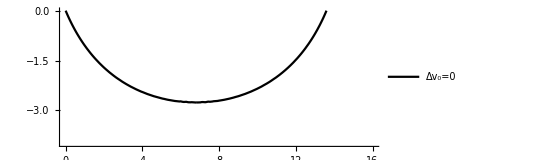

```mathematica
P0=Show[{S1,S2}]
```

#### with decrease in v0 (-0.2)

```mathematica
param1={v0->1.8,G->0.5,p->0.25,epslion->0.2,eta->0.2}
```

{v0→1.8,G→0.5,p→0.25,epslion→0.2,eta→0.2}

```mathematica
Rl/.param1/.z->-k
```

x==-(0.260785 (3.6-0.5 k) k)/((0.958645 √(1-0.0875 (1.8-0.5 k)^2)+0.846463 √(1-0.025 (1.8-0.5 k)^2)) √(1-0.025 (1.8-0.5 k)^2))

```mathematica
Rr/.param1/.z->-k
```

14.1277-x==-(0.260785 (3.6-0.5 k) k)/((0.958645 √(1-0.0875 (1.8-0.5 k)^2)+0.846463 √(1-0.025 (1.8-0.5 k)^2)) √(1-0.025 (1.8-0.5 k)^2))

```mathematica
S11=ContourPlot[x==-(0.26078478696859336 (3.6-0.5 k) k)/((0.9586448768965492 √(1-0.0875 (1.8-0.5 k)^2)+0.8464632301523795 √(1-0.025 (1.8-0.5 k)^2)) √(1-0.025 (1.8-0.5 k)^2)),{x,0,16},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,PlotLegends->Placed[{"Δv_0<0"},Left],ContourStyle->{Directive[Black,Dashed,Thick]}];
```

```mathematica
S22=ContourPlot[14.127662921730284-x==-(0.26078478696859336 (3.6-0.5 k) k)/((0.9586448768965492 √(1-0.0875 (1.8-0.5 k)^2)+0.8464632301523795 √(1-0.025 (1.8-0.5 k)^2)) √(1-0.025 (1.8-0.5 k)^2)),{x,0,16},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,ContourStyle->{Directive[Black,Dashed,Thick]}];
```

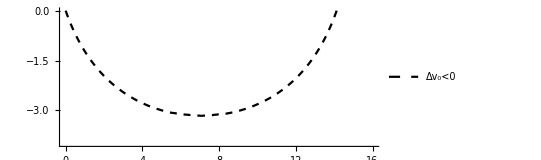

```mathematica
P1=Show[{S11,S22}]
```

#### increase in v0 (+0.2)

```mathematica
param2={v0->2.2,G->0.5,p->0.25,epslion->0.2,eta->0.2}
```

{v0→2.2,G→0.5,p→0.25,epslion→0.2,eta→0.2}

```mathematica
Rl/.param2/.z->-k
```

x==-(0.266652 (4.4-0.5 k) k)/((0.93755 √(1-0.0875 (2.2-0.5 k)^2)+0.759276 √(1-0.025 (2.2-0.5 k)^2)) √(1-0.025 (2.2-0.5 k)^2))

```mathematica
Rr/.param2/.z->-k
```

12.9576-x==-(0.266652 (4.4-0.5 k) k)/((0.93755 √(1-0.0875 (2.2-0.5 k)^2)+0.759276 √(1-0.025 (2.2-0.5 k)^2)) √(1-0.025 (2.2-0.5 k)^2))

```mathematica
S111=ContourPlot[x==-(0.2666524455821211 (4.4-0.5 k) k)/((0.9375499986667378 √(1-0.0875 (2.2-0.5 k)^2)+0.7592759709091287 √(1-0.025 (2.2-0.5 k)^2)) √(1-0.025 (2.2-0.5 k)^2)),{x,0,16},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,PlotLegends->Placed[{"Δv_0>0"},Left],ContourStyle->{Directive[Black,Dotted,Thick]}];
```

```mathematica
S222=ContourPlot[12.95761884893815-x==-(0.2666524455821211 (4.4-0.5 k) k)/((0.9375499986667378 √(1-0.0875 (2.2-0.5 k)^2)+0.7592759709091287 √(1-0.025 (2.2-0.5 k)^2)) √(1-0.025 (2.2-0.5 k)^2)),{x,0,16},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,ContourStyle->{Directive[Black,Dotted,Thick]}];
```

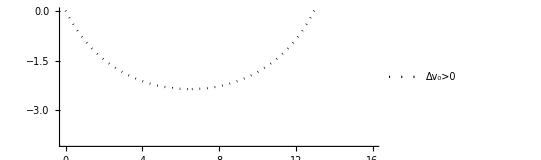

```mathematica
P2=Show[{S111,S222}]
```

## size for the figure is 400*160

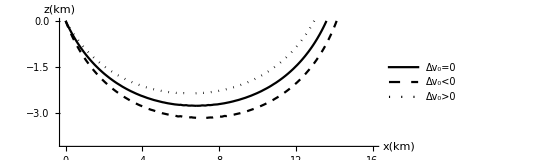

```mathematica
Show[{P0,P1,P2},AxesStyle->Black,AxesLabel->{Style["x(km)",Black,FontSize->20],Style["z(km)",Black,FontSize->20]}]
```

## the diving-wave ray trajectory

#### perturbation in velocity gradient

```mathematica
Clear["Global`*"]
```

#### constant G

```mathematica
S1=ContourPlot[x==-(0.26352313834736496 (4-0.5 k) k)/((0.9486832980505138 √(1-0.0875 (2-0.5 k)^2)+0.806225774829855 √(1-0.025 (2-0.5 k)^2)) √(1-0.025 (2-0.5 k)^2)),{x,0,18},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,PlotLegends->Placed[{"ΔG=0"},Left],ContourStyle->{Directive[Black,Thick]}];
```

```mathematica
S2=ContourPlot[13.597385369580762-x==-(0.26352313834736496 (4-0.5 k) k)/((0.9486832980505138 √(1-0.0875 (2-0.5 k)^2)+0.806225774829855 √(1-0.025 (2-0.5 k)^2)) √(1-0.025 (2-0.5 k)^2)),{x,0,18},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,ContourStyle->{Directive[Black,Thick]}];
```

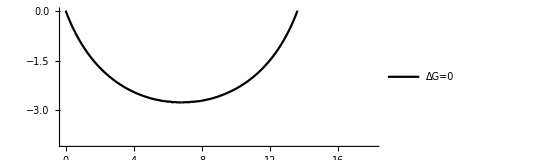

```mathematica
P0=Show[{S1,S2}]
```

#### decrease G -0.1

```mathematica
param3={v0->2,G->0.4,p->0.25,epslion->0.2,eta->0.2}
```

{v0→2,G→0.4,p→0.25,epslion→0.2,eta→0.2}

```mathematica
Rl=x==((1+(2 (epslion-eta))/(1+2 eta)) p z (2 v0+G z))/(√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2)) (√((1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))+√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))))
```

x==((1+(2 (epslion-eta))/(1+2 eta)) p z (2 v0+G z))/(√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2)) (√((1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))+√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))))

```mathematica
Rr=(2 √(1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2))/(G p √(1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2))-x==((1+(2 (epslion-eta))/(1+2 eta)) p z (2 v0+G z))/(√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2)) (√((1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))+√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))))
```

(2 √(1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2))/(G p √(1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2))-x==((1+(2 (epslion-eta))/(1+2 eta)) p z (2 v0+G z))/(√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2)) (√((1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))+√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))))

```mathematica
Rl/.param3/.z->-k
```

x==-(0.263523 (4-0.4 k) k)/((0.948683 √(1-0.0875 (2-0.4 k)^2)+0.806226 √(1-0.025 (2-0.4 k)^2)) √(1-0.025 (2-0.4 k)^2))

```mathematica
Rr/.param3/.z->-k
```

16.9967-x==-(0.263523 (4-0.4 k) k)/((0.948683 √(1-0.0875 (2-0.4 k)^2)+0.806226 √(1-0.025 (2-0.4 k)^2)) √(1-0.025 (2-0.4 k)^2))

```mathematica
S3=ContourPlot[x==-(0.26352313834736496 (4-0.4 k) k)/((0.9486832980505138 √(1-0.0875 (2-0.4 k)^2)+0.806225774829855 √(1-0.025 (2-0.4 k)^2)) √(1-0.025 (2-0.4 k)^2)),{x,0,18},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,PlotLegends->Placed[{"ΔG<0"},Left],ContourStyle->{Directive[Black,Dashed,Thick]}];
```

```mathematica
S4=ContourPlot[16.99673171197595-x==-(0.26352313834736496 (4-0.4 k) k)/((0.9486832980505138 √(1-0.0875 (2-0.4 k)^2)+0.806225774829855 √(1-0.025 (2-0.4 k)^2)) √(1-0.025 (2-0.4 k)^2)),{x,0,18},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,ContourStyle->{Directive[Black,Dashed,Thick]}];
```

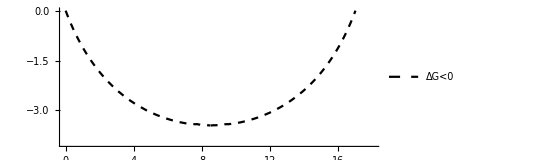

```mathematica
P11=Show[{S3,S4}]
```

#### increase G +0.1

```mathematica
param4={v0->2,G->0.6,p->0.25,epslion->0.2,eta->0.2}
```

{v0→2,G→0.6,p→0.25,epslion→0.2,eta→0.2}

```mathematica
Rl/.param4/.z->-k
```

x==-(0.263523 (4-0.6 k) k)/((0.948683 √(1-0.0875 (2-0.6 k)^2)+0.806226 √(1-0.025 (2-0.6 k)^2)) √(1-0.025 (2-0.6 k)^2))

```mathematica
Rr/.param4/.z->-k
```

11.3312-x==-(0.263523 (4-0.6 k) k)/((0.948683 √(1-0.0875 (2-0.6 k)^2)+0.806226 √(1-0.025 (2-0.6 k)^2)) √(1-0.025 (2-0.6 k)^2))

```mathematica
S33=ContourPlot[x==-(0.26352313834736496 (4-0.6 k) k)/((0.9486832980505138 √(1-0.0875 (2-0.6 k)^2)+0.806225774829855 √(1-0.025 (2-0.6 k)^2)) √(1-0.025 (2-0.6 k)^2)),{x,0,18},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,PlotLegends->Placed[{"ΔG>0"},Left],ContourStyle->{Directive[Black,Dotted,Thick]}];
```

```mathematica
S44=ContourPlot[11.331154474650635-x==-(0.26352313834736496 (4-0.6 k) k)/((0.9486832980505138 √(1-0.0875 (2-0.6 k)^2)+0.806225774829855 √(1-0.025 (2-0.6 k)^2)) √(1-0.025 (2-0.6 k)^2)),{x,0,18},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,ContourStyle->{Directive[Black,Dotted,Thick]}];
```

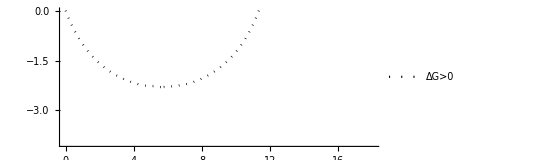

```mathematica
P22=Show[{S33,S44}]
```

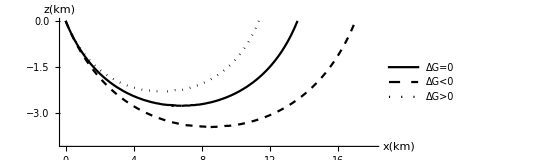

```mathematica
Show[{P0,P11,P22},AxesStyle->Black,AxesLabel->{Style["x(km)",Black,FontSize->20],Style["z(km)",Black,FontSize->20]}]
```

## the diving-wave ray trajectory

#### perturbation in epslion

```mathematica
Clear["Global`*"]
```

```mathematica
Rl=x==((1+(2 (epslion-eta))/(1+2 eta)) p z (2 v0+G z))/(√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2)) (√((1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))+√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))))
```

x==((1+(2 (epslion-eta))/(1+2 eta)) p z (2 v0+G z))/(√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2)) (√((1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))+√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))))

```mathematica
Rr=(2 √(1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2))/(G p √(1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2))-x==((1+(2 (epslion-eta))/(1+2 eta)) p z (2 v0+G z))/(√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2)) (√((1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))+√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))))
```

(2 √(1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2))/(G p √(1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2))-x==((1+(2 (epslion-eta))/(1+2 eta)) p z (2 v0+G z))/(√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2)) (√((1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))+√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))))

#### constant epslion

```mathematica
S1=ContourPlot[x==-(0.26352313834736496 (4-0.5 k) k)/((0.9486832980505138 √(1-0.0875 (2-0.5 k)^2)+0.806225774829855 √(1-0.025 (2-0.5 k)^2)) √(1-0.025 (2-0.5 k)^2)),{x,0,15},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,PlotLegends->Placed[{"Δϵ=0"},Left],ContourStyle->{Directive[Black,Thick]}];
```

```mathematica
S2=ContourPlot[13.597385369580762-x==-(0.26352313834736496 (4-0.5 k) k)/((0.9486832980505138 √(1-0.0875 (2-0.5 k)^2)+0.806225774829855 √(1-0.025 (2-0.5 k)^2)) √(1-0.025 (2-0.5 k)^2)),{x,0,15},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,ContourStyle->{Directive[Black,Thick]}];
```

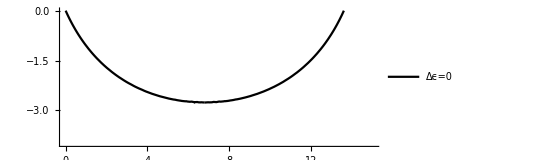

```mathematica
P0=Show[{S1,S2}]
```

#### decrease epslion -0.1

```mathematica
param5={v0->2,G->0.5,p->0.25,epslion->0.1,eta->0.2}
```

{v0→2,G→0.5,p→0.25,epslion→0.1,eta→0.2}

```mathematica
Rl/.param5/.z->-k
```

x==-(0.224105 (4-0.5 k) k)/((0.956183 √(1-0.075 (2-0.5 k)^2)+0.83666 √(1-0.0214286 (2-0.5 k)^2)) √(1-0.0214286 (2-0.5 k)^2))

```mathematica
Rr/.param5/.z->-k
```

14.-x==-(0.224105 (4-0.5 k) k)/((0.956183 √(1-0.075 (2-0.5 k)^2)+0.83666 √(1-0.0214286 (2-0.5 k)^2)) √(1-0.0214286 (2-0.5 k)^2))

```mathematica
S5=ContourPlot[x==-(0.2241053642501988 (4-0.5 k) k)/((0.9561828874675149 √(1-0.075 (2-0.5 k)^2)+0.8366600265340756 √(1-0.02142857142857143 (2-0.5 k)^2)) √(1-0.02142857142857143 (2-0.5 k)^2)),{x,0,15},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,PlotLegends->Placed[{"Δϵ<0"},Left],ContourStyle->{Directive[Black,Dashed,Thick]}];
```

```mathematica
S6=ContourPlot[14.-x==-(0.2241053642501988 (4-0.5 k) k)/((0.9561828874675149 √(1-0.075 (2-0.5 k)^2)+0.8366600265340756 √(1-0.02142857142857143 (2-0.5 k)^2)) √(1-0.02142857142857143 (2-0.5 k)^2)),{x,0,15},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,ContourStyle->{Directive[Black,Dashed,Thick]}];
```

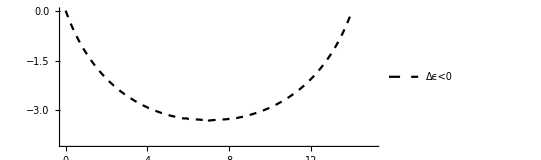

```mathematica
P5=Show[{S5,S6}]
```

#### increase epslion +0.1

```mathematica
param6={v0->2,G->0.5,p->0.25,epslion->0.3,eta->0.2}
```

{v0→2,G→0.5,p→0.25,epslion→0.3,eta→0.2}

```mathematica
Rl/.param6/.z->-k
```

x==-(0.303588 (4-0.5 k) k)/((0.941124 √(1-0.1 (2-0.5 k)^2)+0.774597 √(1-0.0285714 (2-0.5 k)^2)) √(1-0.0285714 (2-0.5 k)^2))

```mathematica
Rr/.param6/.z->-k
```

13.1689-x==-(0.303588 (4-0.5 k) k)/((0.941124 √(1-0.1 (2-0.5 k)^2)+0.774597 √(1-0.0285714 (2-0.5 k)^2)) √(1-0.0285714 (2-0.5 k)^2))

```mathematica
S55=ContourPlot[x==-(0.3035883703594581 (4-0.5 k) k)/((0.9411239481143202 √(1-0.09999999999999999 (2-0.5 k)^2)+0.7745966692414834 √(1-0.02857142857142857 (2-0.5 k)^2)) √(1-0.02857142857142857 (2-0.5 k)^2)),{x,0,15},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,PlotLegends->Placed[{"Δϵ>0"},Left],ContourStyle->{Directive[Black,Dotted,Thick]}];
```

```mathematica
S66=ContourPlot[13.168878268049625-x==-(0.3035883703594581 (4-0.5 k) k)/((0.9411239481143202 √(1-0.09999999999999999 (2-0.5 k)^2)+0.7745966692414834 √(1-0.02857142857142857 (2-0.5 k)^2)) √(1-0.02857142857142857 (2-0.5 k)^2)),{x,0,15},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,ContourStyle->{Directive[Black,Dotted,Thick]}];
```

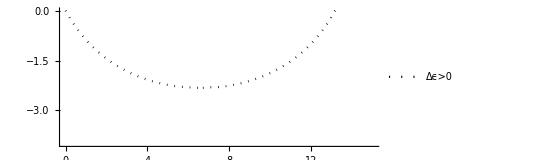

```mathematica
P6=Show[{S55,S66}]
```

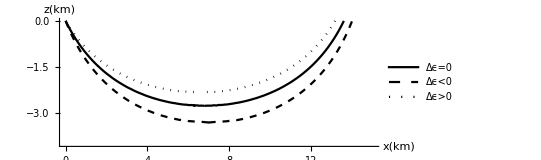

```mathematica
Show[{P0,P5,P6},AxesStyle->Black,AxesLabel->{Style["x(km)",Black,FontSize->20],Style["z(km)",Black,FontSize->20]}]
```

## the diving-wave ray trajectory

#### perturbation in eta

```mathematica
Clear["Global`*"]
```

```mathematica
Rl=x==((1+(2 (epslion-eta))/(1+2 eta)) p z (2 v0+G z))/(√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2)) (√((1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))+√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))))
```

x==((1+(2 (epslion-eta))/(1+2 eta)) p z (2 v0+G z))/(√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2)) (√((1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))+√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))))

```mathematica
Rr=(2 √(1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2))/(G p √(1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2))-x==((1+(2 (epslion-eta))/(1+2 eta)) p z (2 v0+G z))/(√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2)) (√((1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))+√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))))
```

(2 √(1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2))/(G p √(1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2))-x==((1+(2 (epslion-eta))/(1+2 eta)) p z (2 v0+G z))/(√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2)) (√((1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))+√((1-2 eta (1+(2 (epslion-eta))/(1+2 eta)) p^2 v0^2) (1-(1+2 eta) (1+(2 (epslion-eta))/(1+2 eta)) p^2 (v0+G z)^2))))

#### constant delta

```mathematica
S1=ContourPlot[x==-(0.26352313834736496 (4-0.5 k) k)/((0.9486832980505138 √(1-0.0875 (2-0.5 k)^2)+0.806225774829855 √(1-0.025 (2-0.5 k)^2)) √(1-0.025 (2-0.5 k)^2)),{x,0,15},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,PlotLegends->Placed[{"Δη=0"},Left],ContourStyle->{Directive[Black,Thick]}];
```

```mathematica
S2=ContourPlot[13.597385369580762-x==-(0.26352313834736496 (4-0.5 k) k)/((0.9486832980505138 √(1-0.0875 (2-0.5 k)^2)+0.806225774829855 √(1-0.025 (2-0.5 k)^2)) √(1-0.025 (2-0.5 k)^2)),{x,0,15},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,ContourStyle->{Directive[Black,Thick]}];
```

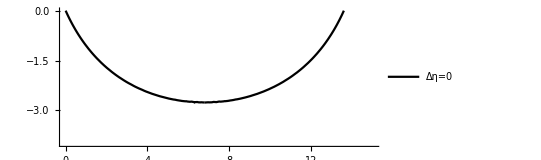

```mathematica
P0=Show[{S1,S2}]
```

#### decrease in eta -0.1

```mathematica
param7={v0->2,G->0.5,p->0.25,epslion->0.2,eta->0.1}
```

{v0→2,G→0.5,p→0.25,epslion→0.2,eta→0.1}

```mathematica
Rl/.param7/.z->-k
```

x==-(0.300565 (4-0.5 k) k)/((0.970395 √(1-0.0875 (2-0.5 k)^2)+0.806226 √(1-0.0145833 (2-0.5 k)^2)) √(1-0.0145833 (2-0.5 k)^2))

```mathematica
Rr/.param7/.z->-k
```

13.2932-x==-(0.300565 (4-0.5 k) k)/((0.970395 √(1-0.0875 (2-0.5 k)^2)+0.806226 √(1-0.0145833 (2-0.5 k)^2)) √(1-0.0145833 (2-0.5 k)^2))

```mathematica
S7=ContourPlot[x==-(0.30056485662556776 (4-0.5 k) k)/((0.9703951085339758 √(1-0.08750000000000001 (2-0.5 k)^2)+0.8062257748298549 √(1-0.014583333333333335 (2-0.5 k)^2)) √(1-0.014583333333333335 (2-0.5 k)^2)),{x,0,15},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,PlotLegends->Placed[{"Δη<0"},Left],ContourStyle->{Directive[Black,Dashed,Thick]}];
```

```mathematica
S8=ContourPlot[13.293154802445125-x==-(0.30056485662556776 (4-0.5 k) k)/((0.9703951085339758 √(1-0.08750000000000001 (2-0.5 k)^2)+0.8062257748298549 √(1-0.014583333333333335 (2-0.5 k)^2)) √(1-0.014583333333333335 (2-0.5 k)^2)),{x,0,15},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,ContourStyle->{Directive[Black,Dashed,Thick]}];
```

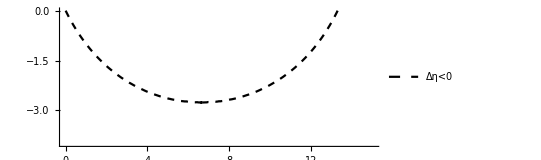

```mathematica
P7=Show[{S7,S8}]
```

#### increase in eta +0.08

```mathematica
param8={v0->2,G->0.5,p->0.25,epslion->0.2,eta->0.3}
```

{v0→2,G→0.5,p→0.25,epslion→0.2,eta→0.3}

```mathematica
Rl/.param8/.z->-k
```

x==-(0.234693 (4-0.5 k) k)/((0.932068 √(1-0.0875 (2-0.5 k)^2)+0.806226 √(1-0.0328125 (2-0.5 k)^2)) √(1-0.0328125 (2-0.5 k)^2))

```mathematica
Rr/.param8/.z->-k
```

13.8398-x==-(0.234693 (4-0.5 k) k)/((0.932068 √(1-0.0875 (2-0.5 k)^2)+0.806226 √(1-0.0328125 (2-0.5 k)^2)) √(1-0.0328125 (2-0.5 k)^2))

```mathematica
S77=ContourPlot[x==-(0.23469327909379628 (4-0.5 k) k)/((0.9320675941153624 √(1-0.08750000000000001 (2-0.5 k)^2)+0.8062257748298549 √(1-0.0328125 (2-0.5 k)^2)) √(1-0.0328125 (2-0.5 k)^2)),{x,0,14},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,PlotLegends->Placed[{"Δη>0"},Left],ContourStyle->{Directive[Black,Dotted,Thick]}];
```

```mathematica
S88=ContourPlot[13.839782091684958-x==-(0.23469327909379628 (4-0.5 k) k)/((0.9320675941153624 √(1-0.08750000000000001 (2-0.5 k)^2)+0.8062257748298549 √(1-0.0328125 (2-0.5 k)^2)) √(1-0.0328125 (2-0.5 k)^2)),{x,0,14},{k,-4,0},Frame->False,Axes->True,AspectRatio->0.4,ContourStyle->{Directive[Black,Dotted,Thick]}];
```

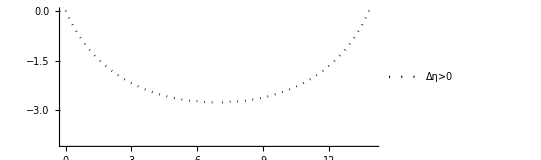

```mathematica
P8=Show[{S77,S88}]
```

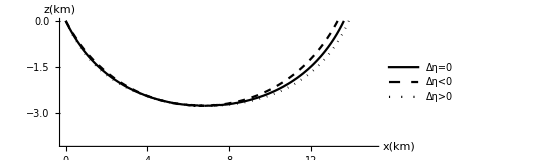

```mathematica
Show[{P0,P7,P8},AxesStyle->Black,AxesLabel->{Style["x(km)",Black,FontSize->20],Style["z(km)",Black,FontSize->20]}]
```